### Description

This notebook imports the results of Eden model simulations for various values of k and ρ and compute the mutant frequency f_MT. f_MT is then fitted and the fit parameters analysed and used for the prediction of how the rate of adaptation varies with environmental parameters.

### Import data

```mathematica
SetDirectory[NotebookDirectory[]<>"/datanersc"];
sListString={"-0.2","-0.1","","0.1","0.2"};
sList={-0.2,-0.1,0,0.1,0.2};
cutoffList={0,0.000001,0.00001,0.0001,0.001,0.01,0.1};
```

```mathematica
fnsAll=Table[GatherBy[SortBy[FileNames["DN-trans-sso-s="<>sListString[[i]]<>"-mutationRate=0.0005_Tfinal=100000_sigma=*_cutoff=0.1_i=*"],StringSplit[#,{"=","_"}][[7]]&],StringSplit[#,{"=","_"}][[7]]&],{i,1,Length@sList}];
fMTvsS01=Table[Table[{sList[[i]],Mean[100000^-1 Total/@Select[Flatten[Import[#,"Table"]&/@fnsAll[[i,j]],1],#[[1]]=="Bubble"&][[All,5;;-1]]]},{i,1,Length@sList}],{j,1,Length@fnsAll[[1]]}];
fnsAll=Table[GatherBy[SortBy[FileNames["DN-trans-sso-s="<>sListString[[i]]<>"-mutationRate=0.0005_Tfinal=100000_sigma=*_cutoff=0.01_i=*"],StringSplit[#,{"=","_"}][[7]]&],StringSplit[#,{"=","_"}][[7]]&],{i,1,Length@sList}];
fMTvsS001=Table[Table[{sList[[i]],Mean[100000^-1 Total/@Select[Flatten[Import[#,"Table"]&/@fnsAll[[i,j]],1],#[[1]]=="Bubble"&][[All,5;;-1]]]},{i,1,Length@sList}],{j,1,Length@fnsAll[[1]]}];
fnsAll=Table[GatherBy[SortBy[FileNames["DN-trans-sso-s="<>sListString[[i]]<>"-mutationRate=0.0005_Tfinal=100000_sigma=*_cutoff=0.001_i=*"],StringSplit[#,{"=","_"}][[7]]&],StringSplit[#,{"=","_"}][[7]]&],{i,1,Length@sList}];
fMTvsS0001=Table[Table[{sList[[i]],Mean[100000^-1 Total/@Select[Flatten[Import[#,"Table"]&/@fnsAll[[i,j]],1],#[[1]]=="Bubble"&][[All,5;;-1]]]},{i,1,Length@sList}],{j,1,Length@fnsAll[[1]]}];
fnsAll=Table[GatherBy[SortBy[FileNames["DN-trans-sso-s="<>sListString[[i]]<>"-mutationRate=0.0005_Tfinal=100000_sigma=*_cutoff=0.0001_i=*"],StringSplit[#,{"=","_"}][[7]]&],StringSplit[#,{"=","_"}][[7]]&],{i,1,Length@sList}];
fMTvsS00001=Table[Table[{sList[[i]],Mean[100000^-1 Total/@Select[Flatten[Import[#,"Table"]&/@fnsAll[[i,j]],1],#[[1]]=="Bubble"&][[All,5;;-1]]]},{i,1,Length@sList}],{j,1,Length@fnsAll[[1]]}];
fnsAll=Table[GatherBy[SortBy[FileNames["DN-trans-sso-s="<>sListString[[i]]<>"-mutationRate=0.0005_Tfinal=100000_sigma=*_cutoff=1e-05_i=*"],StringSplit[#,{"=","_"}][[7]]&],StringSplit[#,{"=","_"}][[7]]&],{i,1,Length@sList}];
fMTvsS000001=Table[Table[{sList[[i]],Mean[100000^-1 Total/@Select[Flatten[Import[#,"Table"]&/@fnsAll[[i,j]],1],#[[1]]=="Bubble"&][[All,5;;-1]]]},{i,1,Length@sList}],{j,1,Length@fnsAll[[1]]}];
fnsAll=Table[GatherBy[SortBy[FileNames["DN-trans-sso-s="<>sListString[[i]]<>"-mutationRate=0.0005_Tfinal=100000_sigma=*_cutoff=1e-06_i=*"],StringSplit[#,{"=","_"}][[7]]&],StringSplit[#,{"=","_"}][[7]]&],{i,1,Length@sList}];
fMTvsS0000001=Table[Table[{sList[[i]],Mean[100000^-1 Total/@Select[Flatten[Import[#,"Table"]&/@fnsAll[[i,j]],1],#[[1]]=="Bubble"&][[All,5;;-1]]]},{i,1,Length@sList}],{j,1,Length@fnsAll[[1]]}];

(*k=0 is handled different because colonies don't always make it to full size*)
fnsAll=Table[GatherBy[SortBy[FileNames["DN-trans-sso-s="<>sListString[[i]]<>"-mutationRate=0.0005_Tfinal=100000_sigma=*_cutoff=0_i=*"],StringSplit[#,{"=","_"}][[7]]&],StringSplit[#,{"=","_"}][[7]]&],{i,1,Length@sList}];
fMTvsS0good=Table[Table[{},{Length@sList}],{Length@fnsAll[[1]]}];
Monitor[For[i=1,i≤Length@sList,i++,{
For[j=1,j≤Length@fnsAll[[1]],j++,{
goodarea0={};
For[k=1,k≤Length@fnsAll[[j,i]],k++,{
area0=Select[Import[fnsAll[[i,j,k]],"Table"],#[[1]]=="Bubble"&][[All,5;;-1]];
goodfns=Quiet@Flatten@Position[Select[Import[fnsAll[[i,j,k]],"Table"],#[[1]]=="Number"&&#[[3]]=="mutations:"&],x_/;x[[5]]==100001];
If[goodfns=={},AppendTo[goodarea0,{{0},{0}}],AppendTo[goodarea0,area0[[goodfns]]]]

}],
fMTvsS0good[[j,i]]={sList[[i]],Mean[100000^-1 Total/@goodarea0[[1]]]}
}]
}],{i,j,k}]//Quiet
fAll={fMTvsS0good,fMTvsS0000001,fMTvsS000001,fMTvsS00001,fMTvsS0001,fMTvsS001,fMTvsS01};
```

```mathematica
obstacleListfMT={0,0.1,0.2,0.3,0.35,0.375,0.4,0.425,0.45,0.5,0.6,0.8}
obstacleListfMT0={0,0.1,0.2,0.3,0.35,0.375,0.39,0.4,0.401,0.4025,0.405,0.4075,0.41,0.4125,0.415,0.425,0.45,0.5,0.6,0.8}
```

{0,0.1,0.2,0.3,0.35,0.375,0.4,0.425,0.45,0.5,0.6,0.8}

{0,0.1,0.2,0.3,0.35,0.375,0.39,0.4,0.401,0.4025,0.405,0.4075,0.41,0.4125,0.415,0.425,0.45,0.5,0.6,0.8}

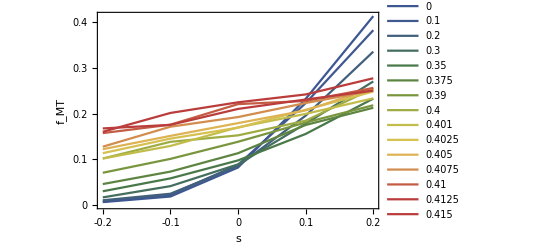

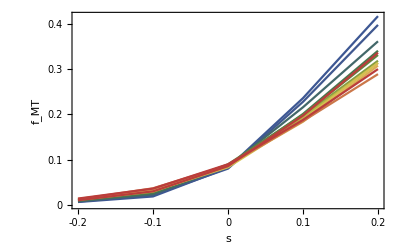

```mathematica
ListLinePlot[fMTvsS0good[[1;;15]],PlotLegends->obstacleListfMT0,PlotStyle->mycolor@15,FrameLabel->{"s","f_MT"},Frame->{True,True,False,False},FrameTicks->myticksfull[0,0.4,5,-0.2,0.2,5],PlotRangePadding->0]
ListLinePlot[fMTvsS01,PlotStyle->mycolor@fMTvsS01,FrameLabel->{"s","f_MT"},Frame->{True,True,False,False},FrameTicks->myticksfull[0,0.4,5,-0.2,0.2,5],PlotRangePadding->0]
```

### Fit f_MT trajectories

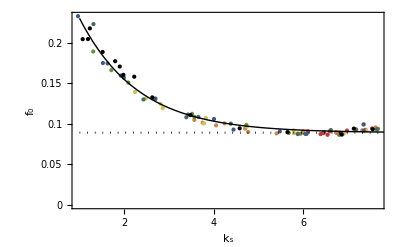

```mathematica
fitsAll=Table[FindFit[If[#[[1,2]]>0.0001,#[[1;;-1]],{{0,0}}],A(*#[[3,2]]*) Exp[b x],{{A,#[[3,2]]},b},x]&/@fAll[[i]],{i,1,Length@fAll}];//Quiet
Show[ListPlot[Reverse@Table[Select[Transpose[Reverse@{A/.fitsAll[[i]],b/.fitsAll[[i]]}],#[[2]]>0&],{i,1,Length@fitsAll}],PlotStyle->Reverse@Join[{Black},mycolor[fitsAll[[1;;-2]]]],FrameLabel->Reverse@{"f_0","k_s"},Joined->False,PlotRange->All,PlotRangePadding->Scaled[.05],FrameTicks->myticksfull[0,0.2,5,1,8,5]],Plot[{A + b Exp[-c y]/.FindFit[Sort@Flatten[Table[Select[Transpose[Reverse@{A/.fitsAll[[i]],b/.fitsAll[[i]]}],#[[2]]>0&],{i,1,Length@fitsAll}],1],0.0005 √(100000/π)+ b Exp[-c x],{{A,0.0005 √(100000/π)},b,c},x],
0.0005 √(100000/π)},{y,1,8},PlotStyle->{{Black,Thick},{Black,Dotted}},PlotRange->All]]//Quiet
```

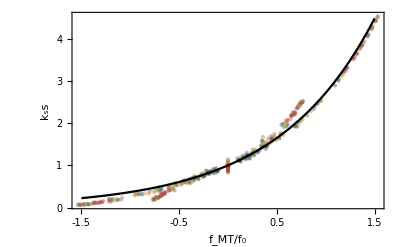

```mathematica
Show[ListPlot[Table[ConstantArray[{b/.fitsAll[[1,i]],1/A/.fitsAll[[1,i]]},Length@#]#&@fAll[[1]][[i]],{i,1,Length@fAll[[1]]}],PlotStyle->{{Opacity[0.4],Black}},Frame->{True,True,False,False},Joined->False,PlotRangePadding->0,PlotRange->{{-1.5,1.5},{0,4.5}},FrameTicks->myticksfull[0,4,5,-1.5,1.5,7],FrameLabel->{"f_MT/f_0","k_ss"}],
Block[{j=2},ListPlot[Table[ConstantArray[{b/.fitsAll[[j,i]],1/A/.fitsAll[[j,i]]},Length@#]#&@fAll[[j]][[i]],{i,1,Length@fAll[[j]]}],PlotStyle->{{Opacity[0.4],mycolor[fitsAll[[1;;-2]]][[j-1]]}},Joined->False]],
Block[{j=3},ListPlot[Table[ConstantArray[{b/.fitsAll[[j,i]],1/A/.fitsAll[[j,i]]},Length@#]#&@fAll[[j]][[i]],{i,1,Length@fAll[[j]]}],PlotStyle->{{Opacity[0.4],mycolor[fitsAll[[1;;-2]]][[j-1]]}},Joined->False]],
Block[{j=4},ListPlot[Table[ConstantArray[{b/.fitsAll[[j,i]],1/A/.fitsAll[[j,i]]},Length@#]#&@fAll[[j]][[i]],{i,1,Length@fAll[[j]]}],PlotStyle->{{Opacity[0.4],mycolor[fitsAll[[1;;-2]]][[j-1]]}},Joined->False]],
Block[{j=5},ListPlot[Table[ConstantArray[{b/.fitsAll[[j,i]],1/A/.fitsAll[[j,i]]},Length@#]#&@fAll[[j]][[i]],{i,1,Length@fAll[[j]]}],PlotStyle->{{Opacity[0.4],mycolor[fitsAll[[1;;-2]]][[j-1]]}},Joined->False]],
Block[{j=6},ListPlot[Table[ConstantArray[{b/.fitsAll[[j,i]],1/A/.fitsAll[[j,i]]},Length@#]#&@fAll[[j]][[i]],{i,1,Length@fAll[[j]]}],PlotStyle->{{Opacity[0.4],mycolor[fitsAll[[1;;-2]]][[j-1]]}},Joined->False]],
Block[{j=7},ListPlot[Table[ConstantArray[{b/.fitsAll[[j,i]],1/A/.fitsAll[[j,i]]},Length@#]#&@fAll[[j]][[i]],{i,1,Length@fAll[[j]]}],PlotStyle->{{Opacity[0.4],mycolor[fitsAll[[1;;-2]]][[j-1]]}},Joined->False]],Plot[Exp[x],{x,-1.5,1.5},PlotStyle->{Black}],PlotRange->All,Joined->True]//Quiet
```

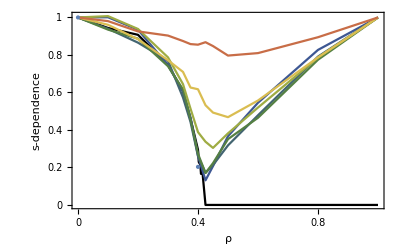

```mathematica
Show[ListLinePlot[Table[Append[Transpose[{If[i>1,obstacleListfMT,obstacleListfMT0],(b/.fitsAll[[i]])/(b/.fitsAll[[i,1]])}],{1,If[i>1,1,0]}],{i,1,Length@fitsAll}],FrameTicks->myticksfull[0,1,5,0,1,5],PlotStyle->Join[{Black},mycolor[fitsAll[[1;;-2]]]],FrameLabel->{"ρ","s-dependence"}],ListPlot[{{0,1},{0.4,2.6/12.8}}],PlotRangePadding->Scaled[.05]]
```

### Compute rate of adaptation

```mathematica
interp0000001=Interpolation[MovingAverage[#,2]&@#]&/@fMTvsS0000001;
interp000001=Interpolation[MovingAverage[#,2]&@#]&/@fMTvsS000001;
interp00001=Interpolation[MovingAverage[#,2]&@#]&/@fMTvsS00001;
interp0001=Interpolation[MovingAverage[#,2]&@#]&/@fMTvsS0001;
interp001=Interpolation[MovingAverage[#,2]&@#]&/@fMTvsS001;
interp01=Interpolation[MovingAverage[#,2]&@#]&/@fMTvsS01;
interp={interp0000001,interp000001,interp00001,interp0001,interp001,interp01};
```

0.000503464

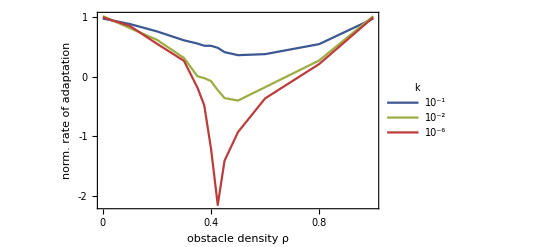

0.00137404

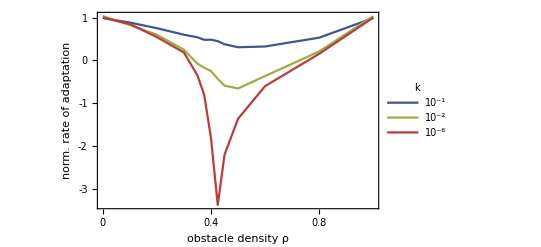

```mathematica
max=Max@#[[All,2]]&@Transpose[{obstacleListfMT,NIntegrate[DFE[0.02,1.3,x]x interp0000001[[#]][x],{x,-0.2,0.2}]&/@Range[Length@interp0000001]}]
ListLinePlot[Reverse@{Append[#,{1,#[[1,2]]}]&@Transpose[{obstacleListfMT,1/max NIntegrate[DFE[0.02,1.3,x]x interp0000001[[#]][x],{x,-0.2,0.2}]&/@Range[Length@interp0000001]}],
Append[#,{1,#[[1,2]]}]&@Transpose[{obstacleListfMT,1/max NIntegrate[DFE[0.02,1.3,x]x interp001[[#]][x],{x,-0.2,0.2}]&/@Range[Length@interp001]}],
Append[#,{1,#[[1,2]]}]&@Transpose[{obstacleListfMT,1/max NIntegrate[DFE[0.02,1.3,x]x interp01[[#]][x],{x,-0.2,0.2}]&/@Range[Length@interp01]}]},PlotStyle->mycolor@3,Frame->{True,True,False,False},AxesStyle->Dotted,FrameLabel->{"obstacle density ρ","norm. rate of adaptation"},FrameTicks->myticksfull[-2,1,5,0,1,6],PlotLegends->Placed[LineLegend[{"10^-1","10^-2","10^-6"},LegendLayout->"Column",LegendLabel->"k"],Scaled@{0.9,0.3}]]
max=Max@#[[All,2]]&@Transpose[{obstacleListfMT,NIntegrate[DFE[0.04,2,x]x interp0000001[[#]][x],{x,-0.2,0.2}]&/@Range[Length@interp0000001]}]
ListLinePlot[Reverse@{Append[#,{1,#[[1,2]]}]&@Transpose[{obstacleListfMT,1/max NIntegrate[DFE[0.04,2,x]x interp0000001[[#]][x],{x,-0.2,0.2}]&/@Range[Length@interp0000001]}],
Append[#,{1,#[[1,2]]}]&@Transpose[{obstacleListfMT,1/max NIntegrate[DFE[0.04,2,x]x interp001[[#]][x],{x,-0.2,0.2}]&/@Range[Length@interp001]}],
Append[#,{1,#[[1,2]]}]&@Transpose[{obstacleListfMT,1/max NIntegrate[DFE[0.04,2,x]x interp01[[#]][x],{x,-0.2,0.2}]&/@Range[Length@interp01]}]},PlotStyle->mycolor@3,Frame->{True,True,False,False},AxesStyle->Dotted,FrameLabel->{"obstacle density ρ","norm. rate of adaptation"},FrameTicks->myticksfull[-3,1,5,0,1,6],PlotLegends->Placed[LineLegend[{"10^-1","10^-2","10^-6"},LegendLayout->"Column",LegendLabel->"k"],Scaled@{0.9,0.3}]]
Plot[DFE[0.02,1.6,x],{x,-0.2,0.2},PlotRange->All]
```

0.000612061

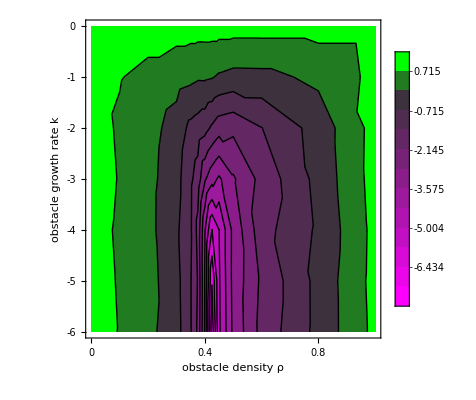

```mathematica
wholeMax=Max@Table[NIntegrate[DFE[0.03,2,x]x interp[[i]][[#]][x],{x,-0.2,0.2}]&/@Range[Length@interp[[6]]],{i,1,6}]
rateOfAdaptation=Table[Append[#,{1,Log10@cutoffList[[i+1]],#[[1,3]]}]&@Transpose[{obstacleListfMT,ConstantArray[Log10@cutoffList[[i+1]],Length@obstacleListfMT], NIntegrate[DFE[0.03,2,x]x interp[[i]][[#]][x],{x,-0.2,0.2}]/wholeMax&/@Range[Length@interp[[i]]]}],{i,1,Length@interp}];
min=Min[Join[Transpose[{Append[obstacleListfMT,1],ConstantArray[0,Length@obstacleListfMT+1],ConstantArray[Max[Flatten[rateOfAdaptation,1][[All,3]]],Length@obstacleListfMT+1]}],Flatten[rateOfAdaptation,1]][[All,3]]];
max=Max[Join[Transpose[{Append[obstacleListfMT,1],ConstantArray[0,Length@obstacleListfMT+1],ConstantArray[Max[Flatten[rateOfAdaptation,1][[All,3]]],Length@obstacleListfMT+1]}],Flatten[rateOfAdaptation,1]][[All,3]]];
ListContourPlot[Join[Transpose[{Append[obstacleListfMT,1],ConstantArray[0,Length@obstacleListfMT+1],ConstantArray[Max[Flatten[rateOfAdaptation,1][[All,3]]],Length@obstacleListfMT+1]}],Flatten[rateOfAdaptation,1]],Contours->((*Create a list of {contour value,graphics directive} pairs.
*If a graphics directive is Null,it will have the default*contour line style.*){#,If[#==0,Directive[Thick,Black],Black(*Replace this if you want to change the default*contour graphics directives.*)]}&/@Join[0-(max-min)/12Range@12,{0},0+(max-min)/12Range@12]),
ColorFunctionScaling->False,InterpolationOrder->3,ColorFunction->(Blend[{{min,Magenta},{0,Hue[0,0,0.2]},{max,Green}},#]&),PlotLegends->Automatic,PlotRangePadding->None,Frame->True,FrameTicks->myticksfull[-6,0,7,0,1,6],FrameTicksStyle->Black,FrameLabel->(Style[#,FontColor->Black]&/@{"obstacle density ρ","obstacle growth rate k"}),BaseStyle->{FontColor->Black,FontSize->14}]
```

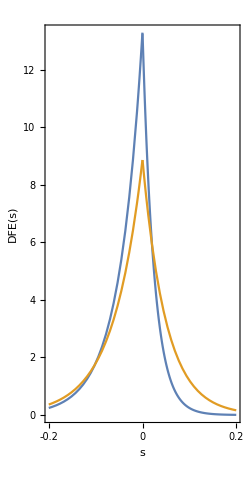

```mathematica
Plot[{DFE[0.025,2,x],DFE[0.05,1.25,x]},{x,-0.2,0.2},FrameLabel->{"s","DFE(s)"},PlotRangePadding->None,Frame->{True,True,False,False},FrameTicks->myticksfull[0,12,7,-0.2,0.2,5],AspectRatio->2,ImageSize->250]
```

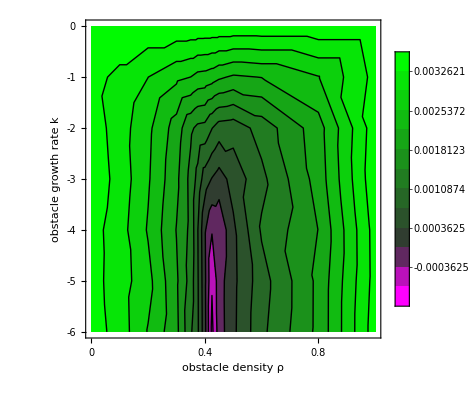

```mathematica
rateOfAdaptation=Table[Append[#,{1,Log10@cutoffList[[i+1]],#[[1,3]]}]&@Transpose[{obstacleListfMT,ConstantArray[Log10@cutoffList[[i+1]],Length@obstacleListfMT], NIntegrate[DFE[0.05,1.25,x]x interp[[i]][[#]][x],{x,-0.2,0.2}]&/@Range[Length@interp[[i]]]}],{i,1,Length@interp}];
min=Min[Join[Transpose[{Append[obstacleListfMT,1],ConstantArray[0,Length@obstacleListfMT+1],ConstantArray[Max[Flatten[rateOfAdaptation,1][[All,3]]],Length@obstacleListfMT+1]}],Flatten[rateOfAdaptation,1]][[All,3]]];
max=Max[Join[Transpose[{Append[obstacleListfMT,1],ConstantArray[0,Length@obstacleListfMT+1],ConstantArray[Max[Flatten[rateOfAdaptation,1][[All,3]]],Length@obstacleListfMT+1]}],Flatten[rateOfAdaptation,1]][[All,3]]];
ListContourPlot[Join[Transpose[{Append[obstacleListfMT,1],ConstantArray[0,Length@obstacleListfMT+1],ConstantArray[Max[Flatten[rateOfAdaptation,1][[All,3]]],Length@obstacleListfMT+1]}],Flatten[rateOfAdaptation,1]],Contours->((*Create a list of {contour value,graphics directive} pairs.
*If a graphics directive is Null,it will have the default*contour line style.*){#,If[#==0,Directive[Thick,Black],Black(*Replace this if you want to change the default*contour graphics directives.*)]}&/@Join[0-(max-min)/12Range@12,{0},0+(max-min)/12Range@12]),
ColorFunctionScaling->False,InterpolationOrder->3,ColorFunction->(Blend[{{min,Magenta},{0,Hue[0,0,0.2]},{max,Green}},#]&),PlotLegends->Automatic,PlotRangePadding->None,Frame->True,FrameTicks->myticksfull[-6,0,7,0,1,6],FrameTicksStyle->Black,FrameLabel->(Style[#,FontColor->Black]&/@{"obstacle density ρ","obstacle growth rate k"}),BaseStyle->{FontColor->Black,FontSize->14}]
```